Info on the notebook:
This notebook uses the BiGONLight package to compute observables in conformal ΛCDM model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight6`"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`70."&);
```

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +γ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+γ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and γ=1 , while for a timelike direction 𝓋^0=±c γ and ψ=c γ β  where β=vel/c the normalized velocity and γ=1/(√(1-β^2)) the Lorentz factor.
import data on files
BGO=<<”BGO_data.m”;
totN=<<”geodesic_data.m”;

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]

StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

# Conformal time ΛCDM

In this notebook we use geometric units G=c=1. This allows us to express mass, length and  time as the same unit. For our convenience, we will express all quantities as dimension-less quantities in units of length L. Therefore, any physical quantity Q^phys=Q^comp L^α where α is a certain exponent and Q^comp is dimensionless. 
L is arbitrary chosen: in particular, we choose to set L equal to the conformal time today in Mpc η_0==L .
From Friedmann equation, η=1/ℋ_0∫(a^(-1/2)ⅆa)/((Ω_m0+Ω_Λ a^3)^(1/2)) , solving the integral and using a_0==1, we finally have L=η_0=14415.175 Mpc
The dimensionless computational present time and the dim-less hubble constant are η_0^comp==η_0/L==1  and  𝒽_0^comp==ℋ_0 L==2.246 10^-4  .
Knowing the conformal time as function of the scale factor η(a), we can use the expression for the redshift in FLRW, 
									z+1=a_𝒪/a 
to find the value of a_in corresponding to a given z_in. Then the initial conformal time is found as η_in==η(a_in).
 Alternatively, one can use a specific value for a_in, like the one we used here  a_in== a_EdS==10^-4.

## Units and Parameters

```mathematica
L=(EllipticF[ArcCos[((1+(1-Sqrt[3])1(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/((H0 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847,H0->67.36/299792.458})) (*Mpc*)

𝒽0=(EllipticF[ArcCos[((1+(1-Sqrt[3])1(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/(( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847})) 
ηin=(EllipticF[ArcCos[((1+(1-Sqrt[3])0.0001(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])0.0001(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/(( 3^(1/4)𝒽0(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847})) 
ETA0=1
```

14415.1749294347

3.23892798946504

0.010996809905677

1

```mathematica
𝒽0/L
67.36/299792.458
```

0.000224688774525475

0.000224688774525475

```mathematica
param={Ωm0->0.3153, ΩΛ->0.6847, c->1}(*arXiv:1807.06209 (Tab 2 5th column) , H0 units: km/s(Mpc)^-1.*)
```

{Ωm0→0.3153,ΩΛ→0.6847,c→1}

## Model set-up

We need to provide the spacetime metric g_μν. 
This can be done in two ways: 
		1)  writing the analytic expression for the metric components g_μν=(g_00 | g_01 | g_02 | g_03
g_10 | g_11 | g_12 | g_13
g_20 | g_21 | g_22 | g_23
g_30 | g_31 | g_32 | g_33) 
		2) import data from a (relativistic) numerical simulation. 
		
In this case, we know the form of the metric g_μν, so we use the first method.

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
Clear[α,β,g,K,g4,X,V,e,Energy,nd,nu,x,y,z,η]
```

```mathematica
X4={η,x,y,z};
X={x,y,z};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, λ};
```

```mathematica
g4={{-(A[η])^2,0,0,0},{0,(A[η])^2,0,0},{0,0,(A[η])^2,0},{0,0,0,(A[η])^2}};
```

```mathematica
solADM=ADM[g4,X4];
α=Evaluate[solADM[[1]]]
β=Evaluate[solADM[[2]]]
g=Evaluate[solADM[[3]]]
K=Evaluate[solADM[[4]]]
nu=Evaluate[solADM[[5]]]
nd=Evaluate[solADM[[6]]]
```

√(A[η]^2)

{0,0,0}

{{A[η]^2,0,0},{0,A[η]^2,0},{0,0,A[η]^2}}

{{-(√(A[η]^2) A'[η])/A[η],0,0},{0,-(√(A[η]^2) A'[η])/A[η],0},{0,0,-(√(A[η]^2) A'[η])/A[η]}}

{1/(√(A[η]^2)),0,0,0}

{-√(A[η]^2),0,0,0}

```mathematica
αα[τ_]:=α/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=g/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
(*αα[η_]:=A[η];
ββ[η_]:={0,0,0};
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[η_]:={{A[η]^2,0,0},{0,A[η]^2,0},{0,0,A[η]^2}};
gg4[η_]:={{-(A[η])^2,0,0,0},{0,(A[η])^2,0,0},{0,0,(A[η])^2,0},{0,0,0,(A[η])^2}};
nup[η_]:={1/(√(A[η]^2)),0,0,0}
ndown[η_]:={-√(A[η]^2),0,0,0}*)
αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
```

## Geodesic

```mathematica
geodBG=GeodesicEquations[X,V,g,K,α,β,η]
```

{x'[η]==√(A[η]^2) v1[η],v1'[η]==√(A[η]^2) (-(2 √(A[η]^2) v1[η] A'[η])/A[η]^3+v1[η] ((√(A[η]^2) v1[η]^2 A'[η])/A[η]+(√(A[η]^2) v2[η]^2 A'[η])/A[η]+(√(A[η]^2) v3[η]^2 A'[η])/A[η])),y'[η]==√(A[η]^2) v2[η],v2'[η]==√(A[η]^2) (-(2 √(A[η]^2) v2[η] A'[η])/A[η]^3+v2[η] ((√(A[η]^2) v1[η]^2 A'[η])/A[η]+(√(A[η]^2) v2[η]^2 A'[η])/A[η]+(√(A[η]^2) v3[η]^2 A'[η])/A[η])),z'[η]==√(A[η]^2) v3[η],v3'[η]==√(A[η]^2) (-(2 √(A[η]^2) v3[η] A'[η])/A[η]^3+v3[η] ((√(A[η]^2) v1[η]^2 A'[η])/A[η]+(√(A[η]^2) v2[η]^2 A'[η])/A[η]+(√(A[η]^2) v3[η]^2 A'[η])/A[η]))}

```mathematica
enereqBG=EnergyEquations[g,K,α,β,Energy,X,V,η]
```

{energy'[η]==√(A[η]^2) energy[η] (-(√(A[η]^2) v1[η]^2 A'[η])/A[η]-(√(A[η]^2) v2[η]^2 A'[η])/A[η]-(√(A[η]^2) v3[η]^2 A'[η])/A[η]),λ'[η]==(√(A[η]^2))/energy[η]}

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
A[η_]:=((Ωm0/ΩΛ)^(1/3)((1-JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])/(-1+√3+(1+√3) JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])))/.param(*from 1109.2258*);

ℋ[η_]=(𝒽0) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.

```mathematica
κ=SetPrecision[𝒱[-1,1,π/4,π/4],70]
```

{-1.,0.5,0.5,0.7071067811865475244008443621048490392848359376884740365883398689953662}

```mathematica
(g4.κ.κ)/.η->ETA0
```

0.

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ϵ=SetPrecision[-∑_(i=1)^4 κ[[i]]nd[[i]]/.{η->ETA0},70]
vi=SetPrecision[Table[(κ[[i]]/ϵ-nu[[i]])/.{η->ETA0},{i,1,4}],70]
```

-1.

{0,-0.4999999999999999999999999999999999999999999999999999999999999999999999,-0.4999999999999999999999999999999999999999999999999999999999999999999999,-0.7071067811865475244008443621048490392848359376884740365883398689953661}

3+1 Initial conditions

```mathematica
substitution={η->ETA0,x->0,y->0,z->0,v2->vi[[3]],v3->vi[[4]]};
```

```mathematica
initialvel1=Flatten[InitialConditions[g,substitution,V,param]]
initialBG=(*{x[ETA0]==0,y[ETA0]==0,v2[ETA0]==0,z[ETA0]==0,v3[ETA0]==0,v1[1]==-1}*)Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[2,2]](*-2.5 10^-4*)(*(V[[1]]/.initialvel1[[2]])*)}]]
E0BG=ϵ(*α/.η->ηin*)(*ϵ*)
initialenergy={Energy[[1]][ETA0]==ϵ,Energy[[2]][ETA0]==1}
```

{v1→-0.5,v1→0.5}

{x[1]==0,y[1]==0,z[1]==0,v2[1]==-0.4999999999999999999999999999999999999999999999999999999999999999999999,v3[1]==-0.7071067811865475244008443621048490392848359376884740365883398689953661,v1[1]==0.5}

-1.

{energy[1]==-1.,λ[1]==1}

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
Timing[solgeodesic=Flatten[SolveGeodesic[geodBG,initialBG,X,V,param,η,ηin,ETA0,"SS",60,60,20,15]]]
```

{5067.65,{x→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],y→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],z→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],v1→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],v2→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],v3→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
Timing[solenergy=Flatten[SolveEnergy[SetPrecision[enereqBG,100],SetPrecision[initialenergy,100],Energy,SetPrecision[solgeodesic,100],SetPrecision[param,100],η,SetPrecision[ηin,100],SetPrecision[ETA0,100],"SS",60,60,20,10]]]
```

{6218.96,{energy→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],λ→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>]}}

Test that the constraint conditions are satisfied for all the evolution

```mathematica
geodesic=Join[solgeodesic,solenergy];
```

Note: 	the solution can be saved in a file as: geodesic >> “file_name.m”.
		Similarly, “.m” files can be imported using the syntax:  geodesic =<<”file_name.m”

```mathematica
Join[solgeodesic,solenergy]>>"LCDM_geodesic_bisect.m"
```

```mathematica
geodesic=<<"LCDM_OtoS_geodesic_45.m"
```

Test the null condition along the geodesic

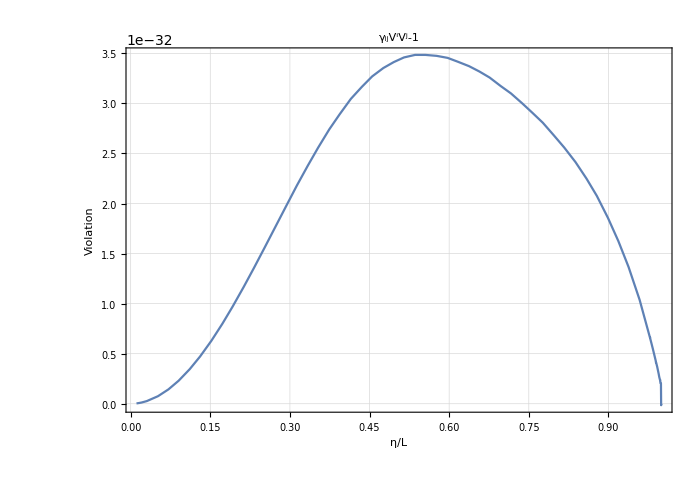

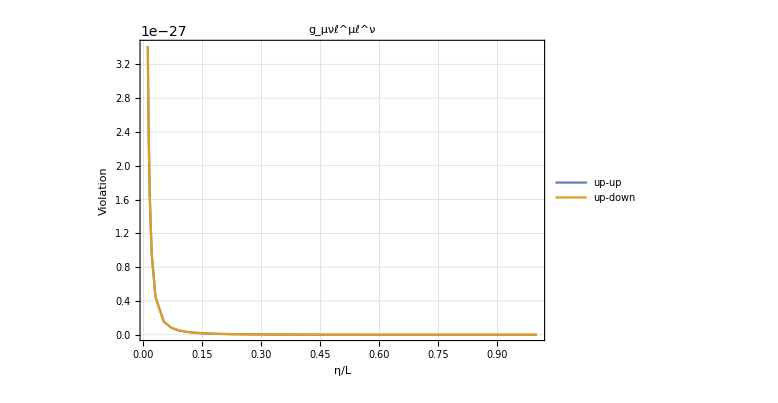

```mathematica
EBG[η_]:=energy[η]/.geodesic;
lup[η_]:=EBG[η](nup[η]+Flatten[{0,VV[η]}]);
ldown[η_]:=EBG[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->60,AspectRatio->0.7,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{gg4[η].lup[η].lup[η],lup[η].ldown[η]}/.geodesic/.param], {η, ηin,ETA0},PlotRange->Full,WorkingPrecision->60,AspectRatio->0.7,ImageSize->Large,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{0.6,0.6}]]]
```

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
redshift[η_]:=EBG[η]/EBG[ETA0]-1
```

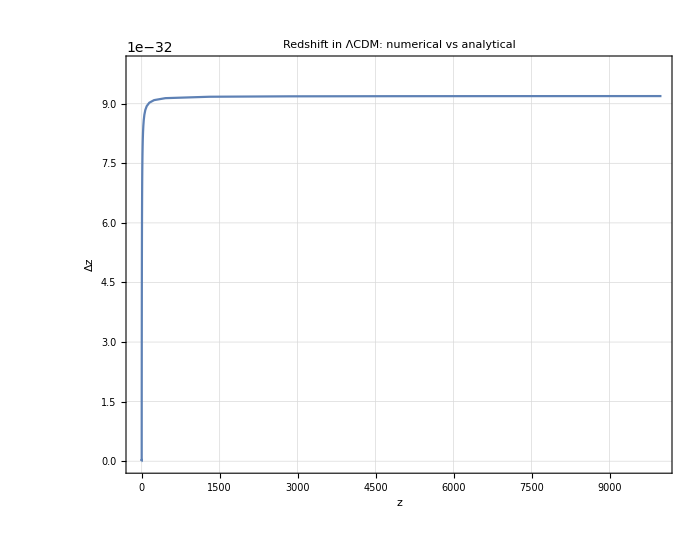

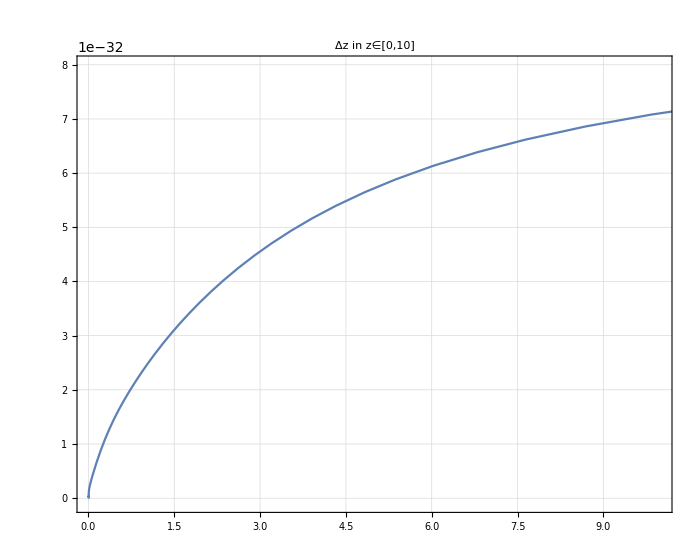

```mathematica
dzplot=ParametricPlot[{redshift[η], Abs[Evaluate[ redshift[η]/(A[ETA0]/A[η]-1)-1]]},{η,ηin,ETA0},WorkingPrecision->40,ImageSize->700,AspectRatio->0.8,PlotRange->{{-100,10000},{-10^-33, 1 10^-31}},Evaluate[StandardPlotStyle[18,24,"Δz","z","Redshift in ΛCDM: numerical vs analytical ",{},{}]]]
plt=ParametricPlot[{redshift[η], Abs[Evaluate[ redshift[η]/(A[ETA0]/A[η]-1)-1]]},{η,ηin,ETA0},WorkingPrecision->40,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{-10^-33, 8 10^-32}},Evaluate[StandardPlotStyle[16,24," "," ","Δz in z∈[0,10]",{},{}]]]
```

Compute the null geodesic

```mathematica
trajectoryBG[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->{{-2,2},{- 2,2},{-2,2}}, ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ]
```

-Graphics3D-

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
```

### set-up the initial conditions for the SNF

```mathematica
(*U={0,0,0};
Γl=Sqrt[1/(1-γ.U.U)]
uu=Γl(nup[η]+Join[{0},U])*)
u[η_]:=SetPrecision[{1/A[η],0,0,0},70]
u[ETA0]//N
u[ηin]//N
```

{1.,0.,0.,0.}

{10000.,0.,0.,0.}

```mathematica
gg4[ETA0].u[ETA0].lup[ETA0]/.Join[geodesic,param]
gg4[η].u[η].u[η]/.η->ETA0
```

1.

-1.

Assuming f_1^μ=OverTilde[f_1]^μ+A u^μ+B k^μ and f_2^μ=OverTilde[f_2]^μ+C u^μ+D k^μ+E f_1^μ, the relations between the vector of the SNF can used to determine the constants A, B, C, D and E.

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
𝒻1=Re[(p1-(gg4[t].p1.lup[t])/(gg4[t].lup[t].u[t])u[t]-1/(gg4[t].lup[t].u[t])((gg4[t].p1.lup[t])/(gg4[t].lup[t].u[t])+gg4[t].p1.u[t])lup[t])/.Join[geodesic,param]/.t->ETA0]
s1=𝒻1/Sqrt[gg4[ETA0].𝒻1.𝒻1]
```

{0.,0.25,0.75,-0.3535533905932737622004221810524245196424179688442370182942}

{0.,0.2886751345948128822545743902509787278238008756350634380093,0.8660254037844386467637231707529361834714026269051903140279,-0.4082482904638630163662140124509818986609912467761116880721}

```mathematica
𝒻2=Re[(p2-(gg4[t].p2.lup[t])/(gg4[t].lup[t].u[t])u[t]-1/(gg4[t].lup[t].u[t])((gg4[t].p2.lup[t])/(gg4[t].lup[t].u[t])+gg4[t].p2.u[t])lup[t]-(gg4[t].p2.s1)s1)/.Join[geodesic,param]/.t->ETA0]
s2=𝒻2/Sqrt[gg4[ETA0].𝒻2.𝒻2]
```

{0.,0.4714045207910316829338962414032326928565572917923160243922,0.,0.3333333333333333333333333333333333333333333333333333333333}

{0.,0.8164965809277260327324280249019637973219824935522233761442,0.,0.577350269189625764509148780501957455647601751270126876019}

Initial conditions for the SN frame

```mathematica
(*u={1/A[η],0,0,0}=> fu0=α u^0 , fu^i=u^i+fu0 β^i/α;
f1=s1=> f10=α s1^0, f1^i=s1^i+f10 β^i/α;
f2=s2=> f20=α s2^0, f2^i=s2^i+f20 β^i/α;
ENW[η_]:=First[Evaluate[energy[η]/.enerNW]];
k[η_]:= Evaluate[(ENW[η](nup[η]+Flatten[{0,VV[η]}]))/.Join[geodesicNW]];
k => fl0=α k^0, fl^i=k^i+fl0 β^i/α ;*)
```

```mathematica
fu0in=(*Cu=*)SetPrecision[((-ndown[t].u[t])/.geodesic/.param)/.t->ETA0,70];
fuin=(*fu^μ=*)SetPrecision[((u[t]-(-ndown[t].u[t]) nup[t])/.geodesic/.param)/.t->ETA0,70];

f10in=(*C1=*)SetPrecision[((-ndown[t].s1)/.geodesic/.param)/.t->ETA0,70];
f1in=(*Subscript[f, 1]^μ=*)SetPrecision[((s1-(-ndown[t].s1) nup[t])/.geodesic/.param)/.t->ETA0,70];

f20in=(*C2=*)SetPrecision[((-ndown[t].s2)/.geodesic/.param)/.t->ETA0,70];
f2in=(*Subscript[f, 2]^μ=*)SetPrecision[((s2-(-ndown[t].s2) nup[t])/.geodesic/.param)/.t->ETA0,70];

fl0in=(*Ck=*)SetPrecision[((-ndown[t].lup[t])/.geodesic/.param)/.t->ETA0,70];(*SetPrecision[A[ηin],∞];*)
flin=(*fk^μ=*)SetPrecision[((lup[t]-(fl0in) nup[t])/.geodesic/.param)/.t->ETA0,70];
```

### Parallel transport the SNF

```mathematica
initialframeBG={{fu0[ETA0]==fu0in,fu1[ETA0]==fuin[[2]],fu2[ETA0]==fuin[[3]] ,fu3[ETA0]==fuin[[4]]},{f10[ETA0]==f10in,f11[ETA0]==f1in[[2]],f12[ETA0]==f1in[[3]],f13[ETA0]==f1in[[4]]},{f20[ETA0]==f20in,f21[ETA0]==f2in[[2]],f22[ETA0]==f2in[[3]],f23[ETA0]==f2in[[4]] },{fl0[ETA0]==fl0in,fl1[ETA0]==flin[[2]],fl2[ETA0]==flin[[3]],fl3[ETA0]==flin[[4]]}};
```

```mathematica
Timing[soltransBG=Flatten[PTransportedFrame[g,K,α,β,solgeodesic,initialframeBG,frame,frame0,param,η,ηin,ETA0,"SS",60,60,20,5]]]
```

{59055.4,{fu1→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fu2→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fu3→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fu0→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f11→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f12→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f13→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f10→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f21→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f22→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f23→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f20→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl1→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl2→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl3→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl0→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
totBG=Flatten[Join[Flatten[soltransBG],solgeodesic]];
```

```mathematica
totBG=<<"LCDM/LCDM_OtoS_ptSNF_45.m"
```

{fu1→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fu2→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fu3→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fu0→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f11→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f12→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f13→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f10→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f21→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f22→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f23→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],f20→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl1→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl2→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl3→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],fl0→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],x→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],y→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],z→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],v1→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],v2→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>],v3→InterpolatingFunction[{{0.0109968099056769648480229754842042091012621853673970352541649, 1.00000000000000000000000000000000000000000000000000000000000}}, <>]}

```mathematica
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryBG[η],{η,ηin,ETA0},PlotRange->{{-2,2},{-2,2},{-2,2}}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{{Red,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pu[η]/.totBG))}],{η,ηin,ETA0,0.05}]},{Green,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(P1[η]/.totBG))}],{η,ηin,ETA0,0.05}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(P2[η]/.totBG))}],{η,ηin,ETA0,0.05}]},{Black,Arrowheads[0.02],Table[Arrow[{trajectoryBG[η],(trajectoryBG[η]+(Pl[η]/.totBG))}],{η,ηin,ETA0,0.05}]}}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
```

-Graphics3D-

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
(*((((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))))/.totBG/.param)*)Q=Re[((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))/.totBG/.param)];
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
```

```mathematica
totBG>>"LCDM_ptSNF_bisect.m"
```

#### Check SNF

-0.57735026630287451474075727918495279118

```mathematica
(gg4[t].u[t].s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].u[t].s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lup[t].s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lup[t].s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s1.s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s1.s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s2.s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lup[t].u[t])/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].u[t].u[t])/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lup[t].lup[t])/.Join[exactgeodesicBG,param]/.t->ηin
```

0.

0.

0.

«2 more identical outputs»

1.

1.

-0.0001

-1.

0.

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

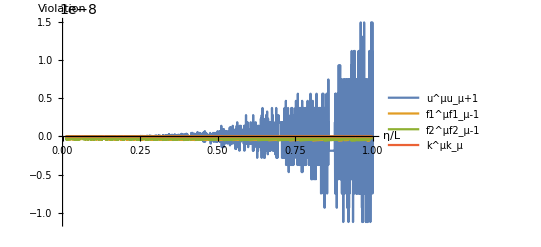

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All(*{-10^-6,10^-6}*)]
```

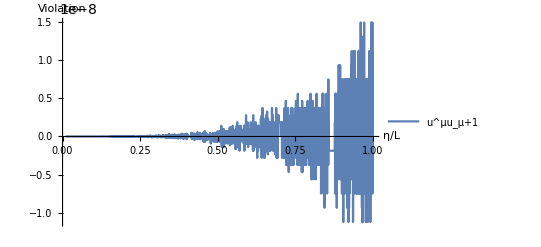

```mathematica
Plot[(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

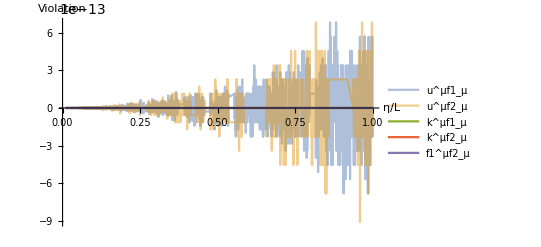

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μf1_μ","u^μf2_μ","k^μf1_μ","k^μf2_μ","f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

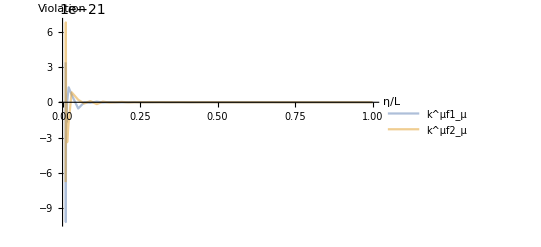

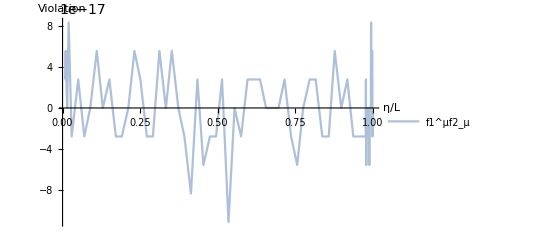

```mathematica
Plot[{(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μf1_μ","k^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
Plot[{(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

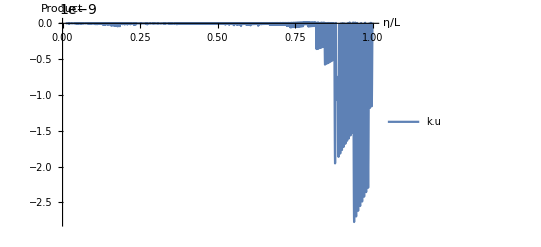

```mathematica
Plot[((((gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])))/((gg4[ηin].(Evaluate[Cu[ηin]nup[ηin]+Flatten[{0, Pu[ηin]}]]).(Evaluate[Cl[ηin]nup[ηin]+Flatten[{0, Pl[ηin]}]]))))/.totBG/.param)-1,{η,ηin,ETA0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All]
```

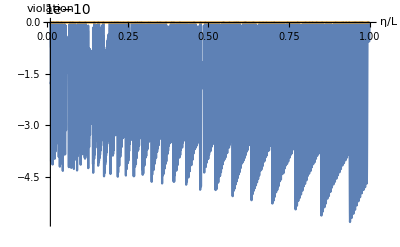

```mathematica
Plot[Evaluate[{(gg[η].VV[η].VV[η]-1),( gg[η].Pl[η].Pl[η]-Cl[η]^2) (*( (gg[η].Pl[η].Pl[η]-Cl[η]^2)/Cl[η]^2) *)}/.totBG/.param], {η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["violation",Large]}]
```

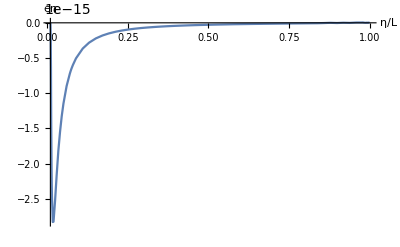

```mathematica
Plot[(A[ηin]^2/A[η]-Cl[η])/.totBG,{η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["en",Large]}]
```

## Optical Tidal Matrix

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,g,K,α,β,η]//Simplify;]
```

{1.09391,Null}

```mathematica
OPT//MatrixForm
```

(0 | 0 | 0 | 0
-f12[η] fu2[η] v1[η]^2 A'[η]^2-f13[η] fu3[η] v1[η]^2 A'[η]^2+f12[η] fu1[η] v1[η] v2[η] A'[η]^2+f11[η] fu2[η] v1[η] v2[η] A'[η]^2-f11[η] fu1[η] v2[η]^2 A'[η]^2-f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu1[η] v1[η] v3[η] A'[η]^2+f11[η] fu3[η] v1[η] v3[η] A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-f11[η] fu1[η] v3[η]^2 A'[η]^2-f12[η] fu2[η] v3[η]^2 A'[η]^2+((f13[η] fu3[η]-f10[η] fu1[η] v1[η]+f10[η] fu0[η] v1[η]^2+f11[η] (fu1[η]-fu0[η] v1[η])-f10[η] fu2[η] v2[η]+f10[η] fu0[η] v2[η]^2+f12[η] (fu2[η]-fu0[η] v2[η])-f13[η] fu0[η] v3[η]-f10[η] fu3[η] v3[η]+f10[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | (-(f11[η]^2+f12[η]^2+f13[η]^2-2 f10[η] f11[η] v1[η]+f10[η]^2 v1[η]^2-2 f10[η] f12[η] v2[η]+f10[η]^2 v2[η]^2-2 f10[η] f13[η] v3[η]+f10[η]^2 v3[η]^2+A[η]^2 (f13[η]^2 (v1[η]^2+v2[η]^2)-2 f11[η] f13[η] v1[η] v3[η]-2 f12[η] v2[η] (f11[η] v1[η]+f13[η] v3[η])+f12[η]^2 (v1[η]^2+v3[η]^2)+f11[η]^2 (v2[η]^2+v3[η]^2))) A'[η]^2+A[η] (f11[η]^2+f12[η]^2+f13[η]^2-2 f10[η] f11[η] v1[η]+f10[η]^2 v1[η]^2-2 f10[η] f12[η] v2[η]+f10[η]^2 v2[η]^2-2 f10[η] f13[η] v3[η]+f10[η]^2 v3[η]^2) A''[η])/A[η]^2 | -f12[η] f22[η] v1[η]^2 A'[η]^2-f13[η] f23[η] v1[η]^2 A'[η]^2+f12[η] f21[η] v1[η] v2[η] A'[η]^2+f11[η] f22[η] v1[η] v2[η] A'[η]^2-f11[η] f21[η] v2[η]^2 A'[η]^2-f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f21[η] v1[η] v3[η] A'[η]^2+f11[η] f23[η] v1[η] v3[η] A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-f11[η] f21[η] v3[η]^2 A'[η]^2-f12[η] f22[η] v3[η]^2 A'[η]^2+((f13[η] f23[η]-f10[η] f21[η] v1[η]+f10[η] f20[η] v1[η]^2+f11[η] (f21[η]-f20[η] v1[η])-f10[η] f22[η] v2[η]+f10[η] f20[η] v2[η]^2+f12[η] (f22[η]-f20[η] v2[η])-f13[η] f20[η] v3[η]-f10[η] f23[η] v3[η]+f10[η] f20[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | 0
-f22[η] fu2[η] v1[η]^2 A'[η]^2-f23[η] fu3[η] v1[η]^2 A'[η]^2+f22[η] fu1[η] v1[η] v2[η] A'[η]^2+f21[η] fu2[η] v1[η] v2[η] A'[η]^2-f21[η] fu1[η] v2[η]^2 A'[η]^2-f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu1[η] v1[η] v3[η] A'[η]^2+f21[η] fu3[η] v1[η] v3[η] A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-f21[η] fu1[η] v3[η]^2 A'[η]^2-f22[η] fu2[η] v3[η]^2 A'[η]^2+((f23[η] fu3[η]-f20[η] fu1[η] v1[η]+f20[η] fu0[η] v1[η]^2+f21[η] (fu1[η]-fu0[η] v1[η])-f20[η] fu2[η] v2[η]+f20[η] fu0[η] v2[η]^2+f22[η] (fu2[η]-fu0[η] v2[η])-f23[η] fu0[η] v3[η]-f20[η] fu3[η] v3[η]+f20[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | -f12[η] f22[η] v1[η]^2 A'[η]^2-f13[η] f23[η] v1[η]^2 A'[η]^2+f12[η] f21[η] v1[η] v2[η] A'[η]^2+f11[η] f22[η] v1[η] v2[η] A'[η]^2-f11[η] f21[η] v2[η]^2 A'[η]^2-f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f21[η] v1[η] v3[η] A'[η]^2+f11[η] f23[η] v1[η] v3[η] A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-f11[η] f21[η] v3[η]^2 A'[η]^2-f12[η] f22[η] v3[η]^2 A'[η]^2+((f13[η] f23[η]-f10[η] f21[η] v1[η]+f10[η] f20[η] v1[η]^2+f11[η] (f21[η]-f20[η] v1[η])-f10[η] f22[η] v2[η]+f10[η] f20[η] v2[η]^2+f12[η] (f22[η]-f20[η] v2[η])-f13[η] f20[η] v3[η]-f10[η] f23[η] v3[η]+f10[η] f20[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2 | (-(f21[η]^2+f22[η]^2+f23[η]^2-2 f20[η] f21[η] v1[η]+f20[η]^2 v1[η]^2-2 f20[η] f22[η] v2[η]+f20[η]^2 v2[η]^2-2 f20[η] f23[η] v3[η]+f20[η]^2 v3[η]^2+A[η]^2 (f23[η]^2 (v1[η]^2+v2[η]^2)-2 f21[η] f23[η] v1[η] v3[η]-2 f22[η] v2[η] (f21[η] v1[η]+f23[η] v3[η])+f22[η]^2 (v1[η]^2+v3[η]^2)+f21[η]^2 (v2[η]^2+v3[η]^2))) A'[η]^2+A[η] (f21[η]^2+f22[η]^2+f23[η]^2-2 f20[η] f21[η] v1[η]+f20[η]^2 v1[η]^2-2 f20[η] f22[η] v2[η]+f20[η]^2 v2[η]^2-2 f20[η] f23[η] v3[η]+f20[η]^2 v3[η]^2) A''[η])/A[η]^2 | 0
-(10000. (-(fu1[η]^2+fu2[η]^2+fu3[η]^2-2 fu0[η] fu1[η] v1[η]+fu0[η]^2 v1[η]^2-2 fu0[η] fu2[η] v2[η]+fu0[η]^2 v2[η]^2-2 fu0[η] fu3[η] v3[η]+fu0[η]^2 v3[η]^2+A[η]^2 (fu3[η]^2 (v1[η]^2+v2[η]^2)-2 fu1[η] fu3[η] v1[η] v3[η]-2 fu2[η] v2[η] (fu1[η] v1[η]+fu3[η] v3[η])+fu2[η]^2 (v1[η]^2+v3[η]^2)+fu1[η]^2 (v2[η]^2+v3[η]^2))) A'[η]^2+A[η] (fu1[η]^2+fu2[η]^2+fu3[η]^2-2 fu0[η] fu1[η] v1[η]+fu0[η]^2 v1[η]^2-2 fu0[η] fu2[η] v2[η]+fu0[η]^2 v2[η]^2-2 fu0[η] fu3[η] v3[η]+fu0[η]^2 v3[η]^2) A''[η]))/A[η]^2 | -10000. (-f12[η] fu2[η] v1[η]^2 A'[η]^2-f13[η] fu3[η] v1[η]^2 A'[η]^2+f12[η] fu1[η] v1[η] v2[η] A'[η]^2+f11[η] fu2[η] v1[η] v2[η] A'[η]^2-f11[η] fu1[η] v2[η]^2 A'[η]^2-f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu1[η] v1[η] v3[η] A'[η]^2+f11[η] fu3[η] v1[η] v3[η] A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-f11[η] fu1[η] v3[η]^2 A'[η]^2-f12[η] fu2[η] v3[η]^2 A'[η]^2+((f13[η] fu3[η]-f10[η] fu1[η] v1[η]+f10[η] fu0[η] v1[η]^2+f11[η] (fu1[η]-fu0[η] v1[η])-f10[η] fu2[η] v2[η]+f10[η] fu0[η] v2[η]^2+f12[η] (fu2[η]-fu0[η] v2[η])-f13[η] fu0[η] v3[η]-f10[η] fu3[η] v3[η]+f10[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2) | -10000. (-f22[η] fu2[η] v1[η]^2 A'[η]^2-f23[η] fu3[η] v1[η]^2 A'[η]^2+f22[η] fu1[η] v1[η] v2[η] A'[η]^2+f21[η] fu2[η] v1[η] v2[η] A'[η]^2-f21[η] fu1[η] v2[η]^2 A'[η]^2-f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu1[η] v1[η] v3[η] A'[η]^2+f21[η] fu3[η] v1[η] v3[η] A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-f21[η] fu1[η] v3[η]^2 A'[η]^2-f22[η] fu2[η] v3[η]^2 A'[η]^2+((f23[η] fu3[η]-f20[η] fu1[η] v1[η]+f20[η] fu0[η] v1[η]^2+f21[η] (fu1[η]-fu0[η] v1[η])-f20[η] fu2[η] v2[η]+f20[η] fu0[η] v2[η]^2+f22[η] (fu2[η]-fu0[η] v2[η])-f23[η] fu0[η] v3[η]-f20[η] fu3[η] v3[η]+f20[η] fu0[η] v3[η]^2) (-A'[η]^2+A[η] A''[η]))/A[η]^2) | 0)

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of fuctions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

#### Use the interpolation to make a better OPT

```mathematica
A[η_]:=((Ωm0/ΩΛ)^(1/3)((1-JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4(*Sqrt[2+Sqrt[3]]/2*)])/(-1+√3+(1+√3) JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4(*Sqrt[2+Sqrt[3]]/2*)])))/.param(*from 1109.2258*);
𝒟[η_]=(A[η]Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.param;
ϕ[x_]=(Amp 3/2 Ωm0/𝒟[ETA0](𝒽0)^2((ω^2(x )^2+2Sin[ω(x )])/(2 ω^2)))/.param;
ℋ[η_]=(𝒽0) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;(*(𝒽0/L) Sqrt[Ωm0/A[η]+ΩΛ A[η]^2]/.param;*)
```

```mathematica
step=(ETA0-ηin)/49999
```

0.00001978045941107468219668347415979911180021076050786221653924748750399389

```mathematica
Simpleℛll[t_]=Evaluate[(EBG[η])^2 OPT/.Join[{η->t},totBG,param]];
```

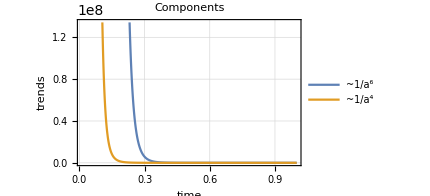
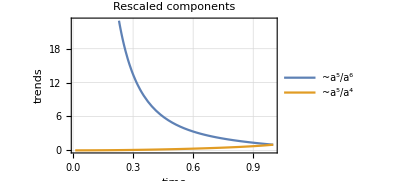
Note: to have a better interpolation, I have decided to multiply by a^5 the components of the (ℛ^μ)_(ℓ ℓ ν). Indeed, computing this matrix in the FLRW metric analytically one observes that some components go like 1/a^6 while others like 1/a^4. These two functions are very steep and this does not allow us to have an accurate interpolation.  Therefore, we can multiply by a^5 all the components to have better functions to interpolate and then, after the interpolation, we can divide by the same quantity.
 -Graphics--Graphics-

```mathematica
Timing[TMP=Table[{τ,A[τ]^5 Simpleℛll[τ]},{τ,ηin,ETA0,step}];]
```

{34574.5,Null}

```mathematica
Timing[tmp00=Table[{TMP[[i,1]],TMP[[i,2]][[1,1]]},{i,1,Length[TMP]}];
tmp01=Table[{TMP[[i,1]],TMP[[i,2]][[1,2]]},{i,1,Length[TMP]}];
tmp02=Table[{TMP[[i,1]],TMP[[i,2]][[1,3]]},{i,1,Length[TMP]}];
tmp03=Table[{TMP[[i,1]],TMP[[i,2]][[1,4]]},{i,1,Length[TMP]}];
tmp10=Table[{TMP[[i,1]],TMP[[i,2]][[2,1]]},{i,1,Length[TMP]}];
tmp11=Table[{TMP[[i,1]],TMP[[i,2]][[2,2]]},{i,1,Length[TMP]}];
tmp12=Table[{TMP[[i,1]],TMP[[i,2]][[2,3]]},{i,1,Length[TMP]}];
tmp13=Table[{TMP[[i,1]],TMP[[i,2]][[2,4]]},{i,1,Length[TMP]}];
tmp20=Table[{TMP[[i,1]],TMP[[i,2]][[3,1]]},{i,1,Length[TMP]}];
tmp21=Table[{TMP[[i,1]],TMP[[i,2]][[3,2]]},{i,1,Length[TMP]}];
tmp22=Table[{TMP[[i,1]],TMP[[i,2]][[3,3]]},{i,1,Length[TMP]}];
tmp23=Table[{TMP[[i,1]],TMP[[i,2]][[3,4]]},{i,1,Length[TMP]}];
tmp30=Table[{TMP[[i,1]],TMP[[i,2]][[4,1]]},{i,1,Length[TMP]}];
tmp31=Table[{TMP[[i,1]],TMP[[i,2]][[4,2]]},{i,1,Length[TMP]}];
tmp32=Table[{TMP[[i,1]],TMP[[i,2]][[4,3]]},{i,1,Length[TMP]}];
tmp33=Table[{TMP[[i,1]],TMP[[i,2]][[4,4]]},{i,1,Length[TMP]}];]
```

{3.42978,Null}

```mathematica
TMP>>"LCDM_res49999_TMP_bisect.m"
```

```mathematica
tmp[t_]=({{Interpolation[tmp00,InterpolationOrder->10][t],Interpolation[tmp01,InterpolationOrder->10][t],Interpolation[tmp02,InterpolationOrder->10][t],Interpolation[tmp03,InterpolationOrder->10][t]},{Interpolation[tmp10,InterpolationOrder->10][t],Interpolation[tmp11,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t], Interpolation[tmp13,InterpolationOrder->10][t]},{Interpolation[tmp20,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t],Interpolation[tmp22,InterpolationOrder->10][t], Interpolation[ tmp23,InterpolationOrder->10][t]},{Interpolation[tmp30,InterpolationOrder->10][t],Interpolation[tmp31,InterpolationOrder->10][t],Interpolation[tmp32,InterpolationOrder->10][t],Interpolation[tmp33,InterpolationOrder->10][t]}});
```

```mathematica
ℛll[t_]=A[t]^-5 tmp[t];
```

```mathematica
(ℛll[t]/.t->0.9)//MatrixForm
(Simpleℛll[t]/.t->0.9)//MatrixForm
(Aℛab[t]/.t->0.9)//MatrixForm
```

(0 | 0 | 0 | 0
0. | -22.643824749016819379256492358387215087008952178482668738 | 0. | 0
0. | 0. | -22.643824749016819379256492358387215087008952178482668738 | 0
3.070547440904300166058955479781546762529969422185205491 | 0. | 0. | 0)

(0 | 0 | 0 | 0
0. | -22.6438247490168193792564923583872150937740969035680651452 | 0. | 0
0. | 0. | -22.6438247490168193792564923583872150937740969035680651452 | 0
3.0705474409043001660589554797815467635106155640272174325 | 0. | 0. | 0)

(0 | 0 | 0 | 0
0 | -22.64382474901681937925649235838659292622519948234685120222 | 0 | 0
0 | 0 | -22.64382474901681937925649235838659292622519948234685120222 | 0
3.070547440904300166058955479781462224703173488298878388471 | 0 | 0 | 0)

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
```

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ETA0]==0,Mll[[i,j]][ETA0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{67.6686,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ETA0]==KroneckerDelta[i,j],Mlx[[i,j]][ETA0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{72.4422,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
BGO>>"LCDM_res49999_BGO_bisect.m";
```

```mathematica
𝒲[ηin]//N//MatrixForm

111111111111111111111111111111111111111111111111111111111111111111111111111111111111
𝒲[ETA0]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 0.000420331 | 0. | 0.
0. | 0. | 0.000420331 | 0.
0.0272089 | 0. | 0. | 1.) | (0.162773 | 0. | 0. | 0.
0. | 0.0000989003 | 0. | 0.
0. | 0. | 0.0000989003 | 0.
-0.00133504 | 0. | 0. | 0.162773)
(0. | 0. | 0. | 0.
0. | -7.61221×10^6 | 0. | 0.
0. | 0. | -7.61221×10^6 | 0.
-178.632 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -1.78871×10^6 | 0. | 0.
0. | 0. | -1.78871×10^6 | 0.
-29.1036 | 0. | 0. | 1.))

111111111111111111111111111111111111111111111111111111111111111111111111111111111111

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
tmpWAB=SetPrecision[Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}],50];
```

```mathematica
detWxlAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t],50];
```

Here we are in synchronous-comoving gauge, meaning that all elements are comoving with respect to the cosmic expansion. In this case the observer four-velocity u^μ is equal to the normal n^μ to the foliation. In general, in other coordinates, we should take into account that the observer has a proper velocity which induce an aberration effect due to its motion: this is the described by the term g_μν ℓ^μ u^ν|_𝒪

```mathematica
(*Uvel[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG*)
```

```mathematica
DangWxl[η_]=Evaluate[(gg4[ETA0].lup[ETA0].(nup[ETA0]))Evaluate[detWxlAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
```

0.

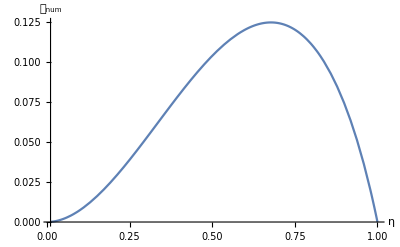

```mathematica
Plot[DangWxl[η] ,{η,ηin,ETA0},WorkingPrecision->30,AxesLabel->{"η","𝒟_num"}]
```

In ΛCDM the angular diameter distance as function of the redshift is:

```mathematica
χz[z_]=Evaluate[1/(1+z)(1/(𝒽0 Ωm0^(1/3)ΩΛ^(1/6) 3^(1/4))(EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+((Ωm0/ΩΛ)^(1/3)(1+z)))-1],(2+Sqrt[3])/4]-EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+(Ωm0/ΩΛ)^(1/3))-1],(2+Sqrt[3])/4]))//.param];
```

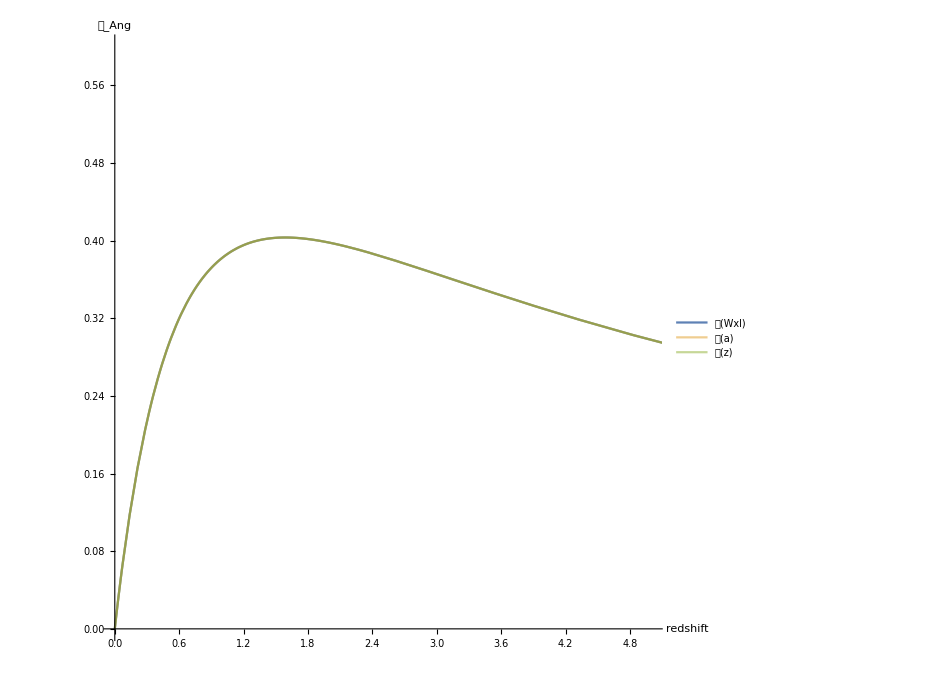

```mathematica
ParametricPlot[{{redshift[η],𝒽0 DangWxl[η]},{redshift[η],𝒽0 χz[redshift[η]]}},{η,ηin,ETA0},PlotRange->{{0,5},{0,0.6}},PlotStyle->{Thick, Opacity[0.5],Opacity[0.5]},AspectRatio->1,ImageSize->700,PlotLegends->{Style["𝒟(Wxl)",Large],Style["𝒟(a)",Large],Style["𝒟(z)",Large]},AxesLabel->{Style["redshift",Large],Style["𝒟_Ang",Large]}]
```

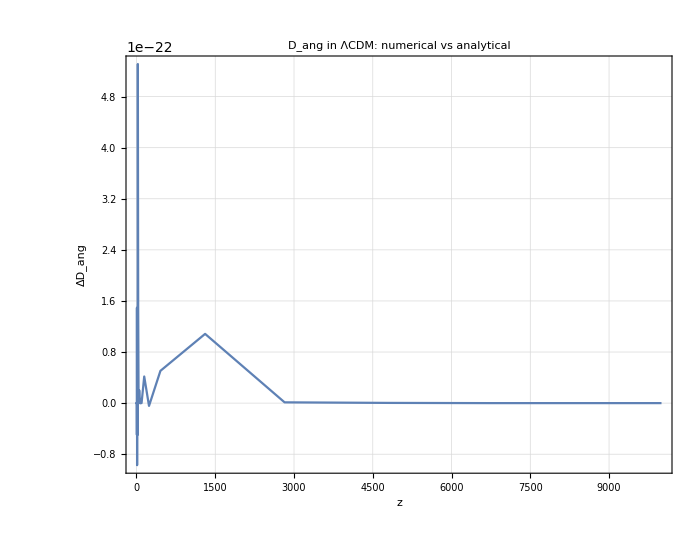

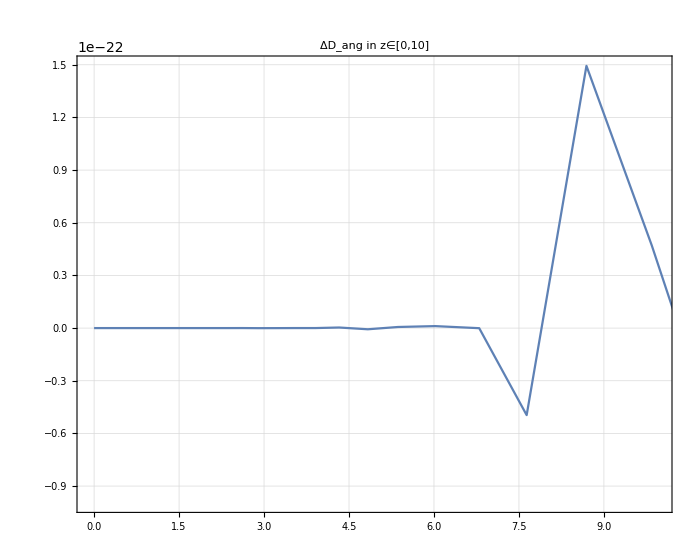

```mathematica
(*{redshift[η], Abs[ (DangWxl2[η]-(χz[redshift[η]]/(1+redshift[η])))/(χz[redshift[η]]/(1+redshift[η]))]}*)
(*LCDMdD=*)ParametricPlot[{redshift[η],  (DangWxl[η]-(  χz[redshift[η]]))/(  χz[redshift[η]])},{η,ηin,ETA0},PlotRange->All(*{{0,10},{0,2 10^-23}}*),ImageSize->700,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24,"ΔD_ang","z","D_ang in ΛCDM: numerical vs analytical",{},{}]], WorkingPrecision->48]
ParametricPlot[{redshift[η],  (DangWxl[η]-(  χz[redshift[η]]))/(  χz[redshift[η]])},{η,ηin,ETA0},PlotRange->{{-0.1,10},{-10^-22,1.5 10^-22}},ImageSize->700,AspectRatio->0.8,Evaluate[StandardPlotStyle[18,24," "," "," ΔD_ang in z∈[0,10] ",{},{}]], WorkingPrecision->48]
```

### Luminosity distance and Parallax distance and the distance slip

```mathematica
(*𝒲[t_]:=𝒲2[t]*)
```

```mathematica
Timing[tmpWAA=SetPrecision[Table[𝒲[η][[1,1]][[i,j]],{i,2,3},{j,2,3}],50];]
```

{0.005216,Null}

```mathematica
Timing[detWxxAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAA])]]]/.η->t],50];]
```

{0.033076,Null}

```mathematica
Dpar[η_]=Evaluate[(gg4[ETA0].lup[ETA0].nup[ETA0])Evaluate[detWxlAB[η]/detWxxAB[η]]/.Join[param,totBG]];
```

```mathematica
DangWxl[ETA0]
Dpar[ETA0]
```

0.

0.

```mathematica
Dlum[t_]=(1+redshift[t])^2 DangWxl[t];
```

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.5}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in ΛCDM model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

```mathematica
ParametricPlot[{{redshift[t], 𝒽0 DangWxl[t]},{redshift[t],𝒽0 Dlum[t]},{redshift[t],𝒽0 Dpar[t]}} ,{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,5},{0,15}},Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in ΛCDM model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

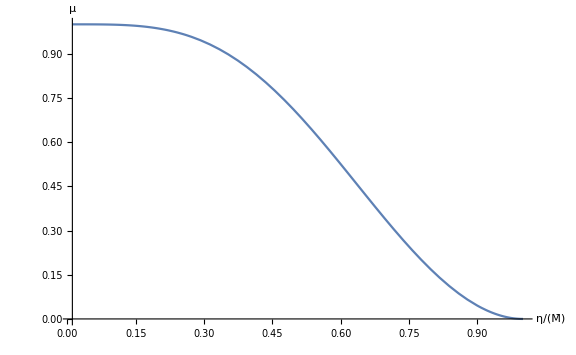

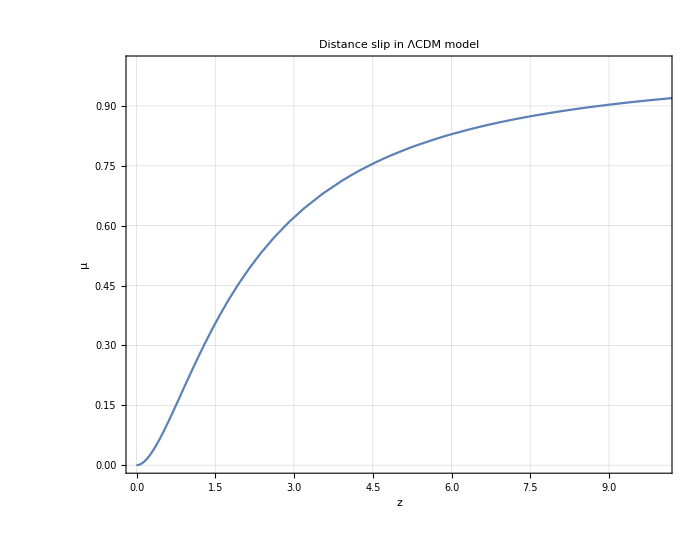

```mathematica
Plot[1-DangWxl[t]^2/Dpar[t]^2 ,{t,ηin,ETA0},WorkingPrecision->30,AxesLabel->{Style["η/(M̄)",Large],Style["μ",Large]},ImageSize->Large]
ParametricPlot[{redshift[t], 1-DangWxl[t]^2/Dpar[t]^2},{t,ηin,ETA0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->{{0,10},{0,1.005}},Evaluate[StandardPlotStyle[18,24,"μ","z","Distance slip in ΛCDM model",{ },{ }]]]
```

### Redshift drift effects

```mathematica
𝒲XX[η_]:=Mxx/.functional[η];
𝒲LX[η_]:=Mlx/.functional[η];
𝒲XL[η_]:=Mxl/.functional[η];
𝒲LL[η_]:=Mll/.functional[η];
I𝒲XL[η_]:=Inverse[𝒲XL[η]];
```

```mathematica
Uoo[η_]:=-hDD.I𝒲XL[η].𝒲XX[η]
Uoe[η_]:=hDD.I𝒲XL[η]
Ueo[η_]:=-(hDD.𝒲LX[η]-hDD.𝒲LL[η].I𝒲XL[η].𝒲XX[η])
Uee[η_]:= -hDD.𝒲LL[η].I𝒲XL[η]
```

```mathematica
𝒰dd[η_]:= {{Uoo[η],Uoe[η]},{Ueo[η],Uee[η]}}
```

```mathematica
(*four acceleration can be calculated as a^ν==u^μ∇_μ u^ν*)
```

```mathematica
up={1/𝒶[η],0,0,0}(*{u0[η],u1[η],u2[η],u3[η]}*);
Table[Sum[(up[[j]]D[up[[i]],X4[[j]]]),{j,1,4}]+Sum[Christoffel[{{-(𝒶[η])^2,0,0,0},{0,(𝒶[η])^2,0,0},{0,0,(𝒶[η])^2,0},{0,0,0,(𝒶[η])^2}},X4][[i,j,s]]up[[j]]up[[s]],{j,1,4},{s,1,4}]//Simplify,{i,1,4}]
```

{0,0,0,0}

Note: the source and observer four-velocity and acceleration have to be projected in the parallel transported frame, since the BGO 𝒲 are expressed in the SNF.

```mathematica
e0[s_]=ldown[s]/Q;
e1[η_]=gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totBG;
e2[η_]=gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totBG;
e3[η_]=(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+e0[η])/Q/.totBG;
```

```mathematica
up[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
```

```mathematica
uE[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aE[η_]:={0,0,0,0}
uO[η_]:={1/A[η],0,0,0}
aO[η_]:={0,0,0,0}
```

```mathematica
ΞDoppler[η_]:=(ldown[η]/(uE[η].ldown[η])).(aE[η]/(1+redshift[η]))-(ldown[ETA0]/(uO[ETA0].ldown[ETA0])).aO[ETA0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[ETA0].ldown[ETA0])(Uoo[η].uO[ETA0].uO[ETA0]+1/(1+redshift[η])Uoe[η].uO[ETA0].uE[η]+1/(1+redshift[η])Ueo[η].uE[η].uO[ETA0]+1/(1+redshift[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

Dimensions: we want to give physical units to our dimensionless redshift drift. To do so, we need to convert L in the unit we want to use, i.e. in 1/s, using c and G.
							s^-1=(Mpc/s)/Mpc=[c/L]=(299792458 3.24078 10^-23)/L

```mathematica
cL=(299792458 3.24078 10^-23)/L(*c/L==(Mpc/s)/Mpc=1/s*)
```

6.73985162714454797289109821229927708517372021951910376936464821697556×10^-19

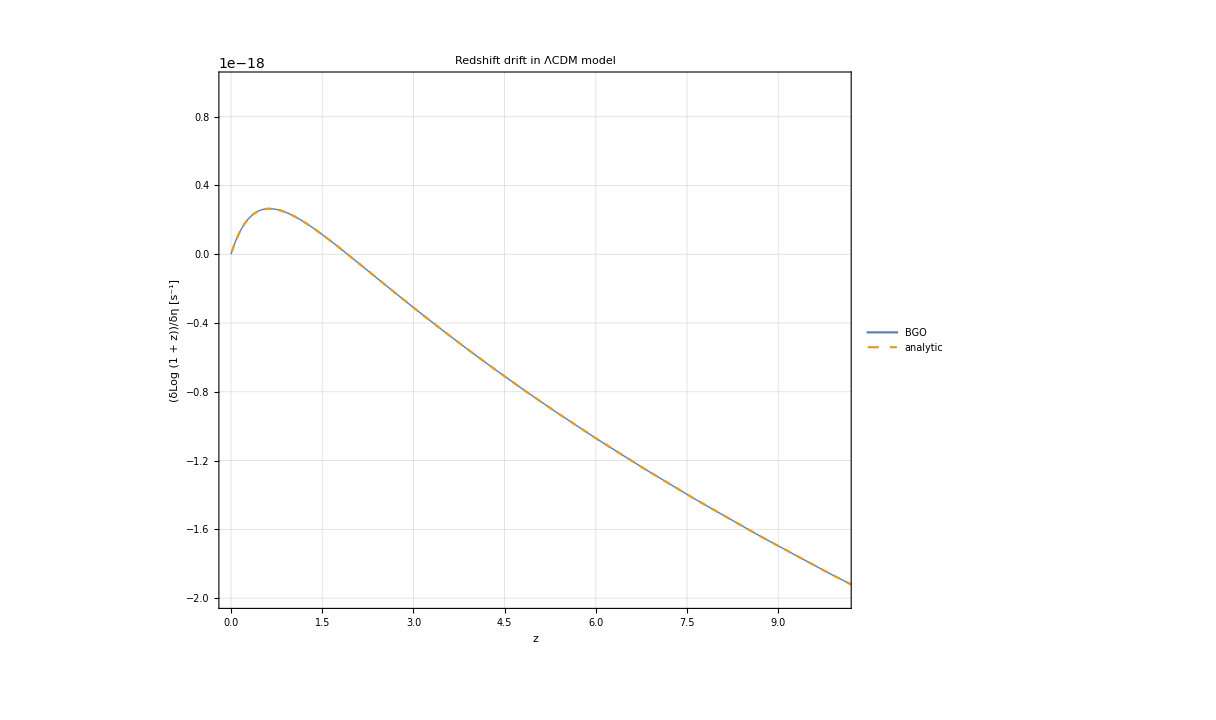

```mathematica
ParametricPlot[{{redshift[t],cL 𝒽0/(1+redshift[t])((1+redshift[t])-Sqrt[Ωm0(1+redshift[t])^3+ΩΛ])/.param},{redshift[t],cL lnzdrift[t]}},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0,10},{-2 10^-18, 10^-18}},AspectRatio->0.8,PlotStyle->{Thick,Dashed},Evaluate[StandardPlotStyle[20,24,"(δLog (1 + z))/δη [s^-1]","z","Redshift drift in ΛCDM model",{"BGO","analytic" },{0.8,0.8 }]]]
```

```mathematica
ANALITICzdrift[t_]:=𝒽0/(1+redshift[t])((1+redshift[t])-Sqrt[Ωm0(1+redshift[t])^3+ΩΛ])/.param
```

```mathematica
ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,ηin,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->60,Evaluate[StandardPlotStyle[20,24,"Δz_drift","z","Redshift drift in ΛCDM model: BGO vs analytical",{},{}]]]
ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0,10},{-2.5 10^-24,2.5 10^-24}},AspectRatio->0.8,WorkingPrecision->60,Evaluate[StandardPlotStyle[20,24,"","","Redshift drift in z∈[0,10]",{},{}]]]
Graphics[{White,Rectangle[]}]
```

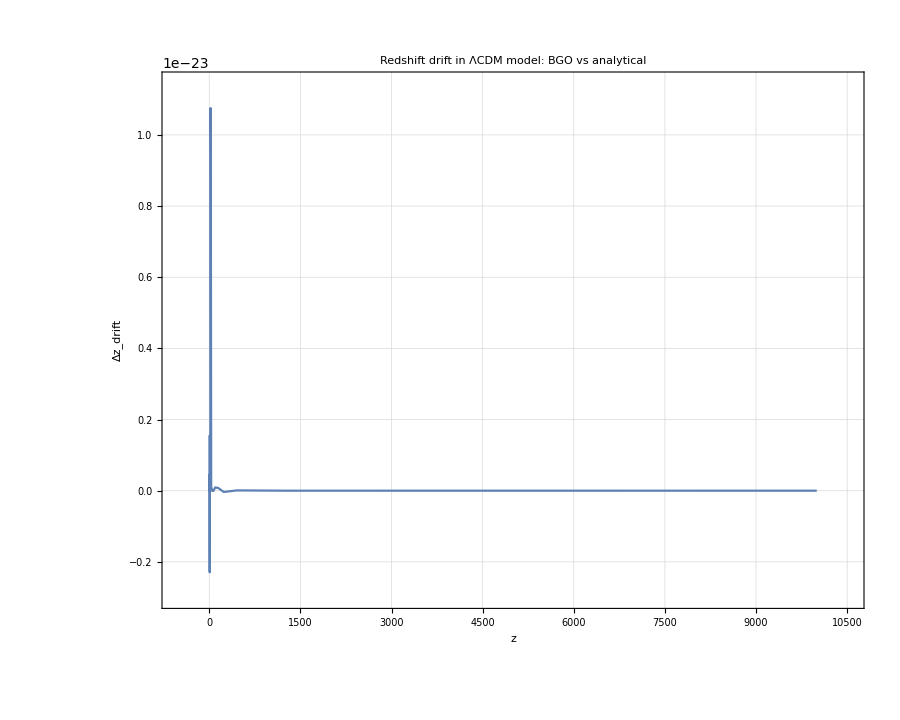

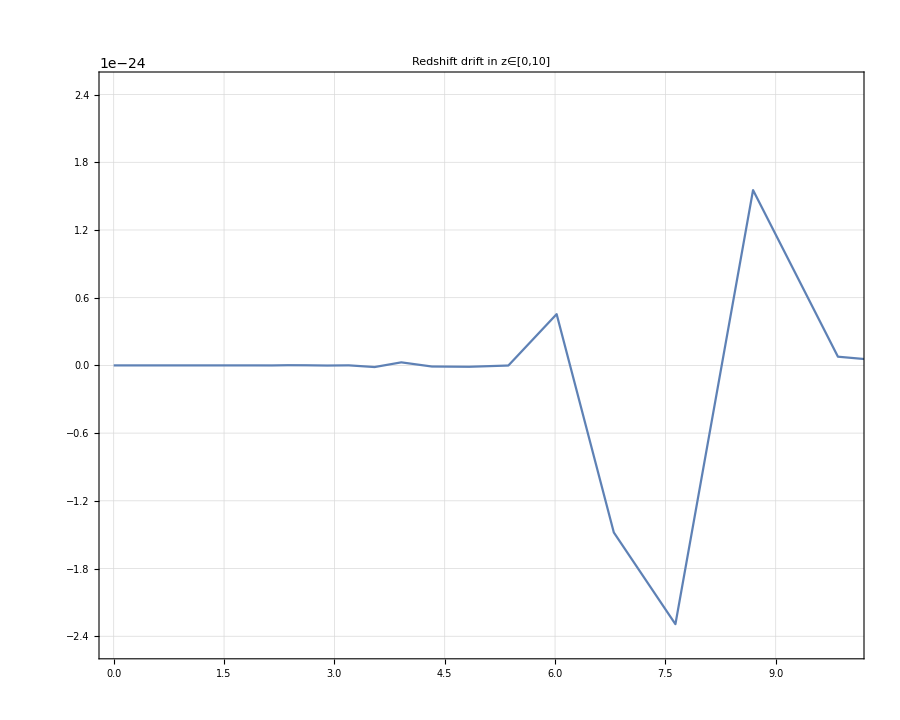

The observables are saved as output

```mathematica
{zLCDM->(Evaluate[redshift[#]]&),DangLCDM->(Evaluate[DangWxl[#]]&) ,DlumLCDM->(Evaluate[Dlum[#]]&) , DparLCDM->(Evaluate[Dpar[#]]&) , ZdriftLCDM->(Evaluate[lnzdrift[#]]&) }>>"observables_LCDM_bisect.m"
```

### Shear and expansion

```mathematica
Timing[tmpWllAB=SetPrecision[Table[𝒲[η][[2,2]][[i,j]],{i,2,3},{j,2,3}],50];]
IWxlAB=Inverse[tmpWAB];
```

{748.61,Null}

```mathematica
trxlll[t_]=SetPrecision[Evaluate[Tr[IWxlAB.tmpWllAB]/.η->t],50];
```

```mathematica
DDang[t_]=1/2 DangWxl[t] trxlll[t];
```

```mathematica
𝒮[t_]=Evaluate[(tmpWllAB.IWxlAB)//.η->t];
```

```mathematica
expansion[η_]=Tr[𝒮[η]]/2;
shear[η_]=Sqrt[(Tr[𝒮[η].𝒮[η]]/2-(Tr[𝒮[η]]/2)^2)];
```

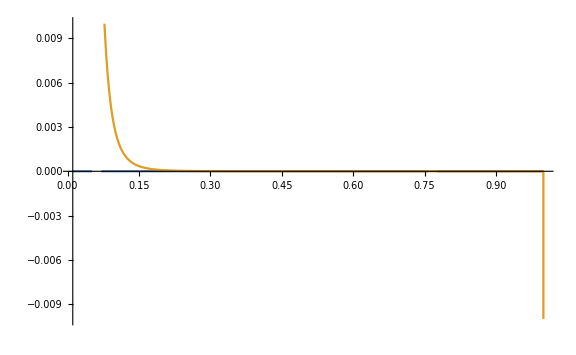

```mathematica
Plot[{shear[η],expansion[η]},{η,ηin,ETA0},ImageSize->Large,PlotRange->0.01]
```

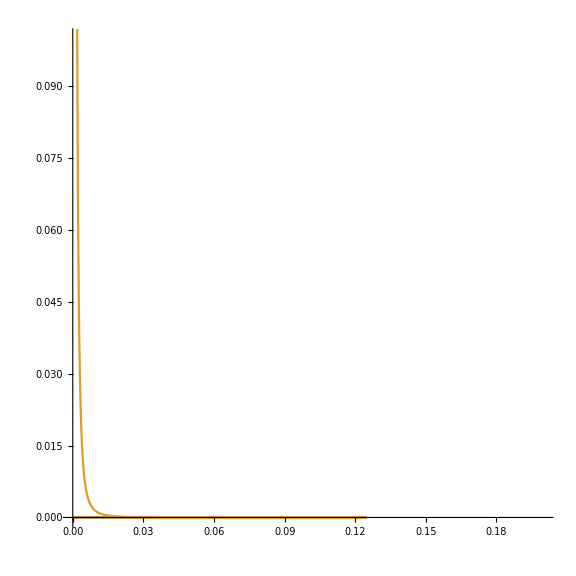

```mathematica
ParametricPlot[{{DangWxl[η], shear[η]},{DangWxl[η],expansion[η]}},{η,ηin,ETA0},ImageSize->Large,PlotRange->{{0,0.2},{0,0.1}}(*{{DangWxl[ETA0], DangWxl[ηin]},{-1,1}}*),AspectRatio->1]
```

#### Deviation (to be fixed)

```mathematica
δx={0,0,-10^-6/8,-10^-6/8};
δXf[t_]=𝒲[t][[1,2]].δx;
```

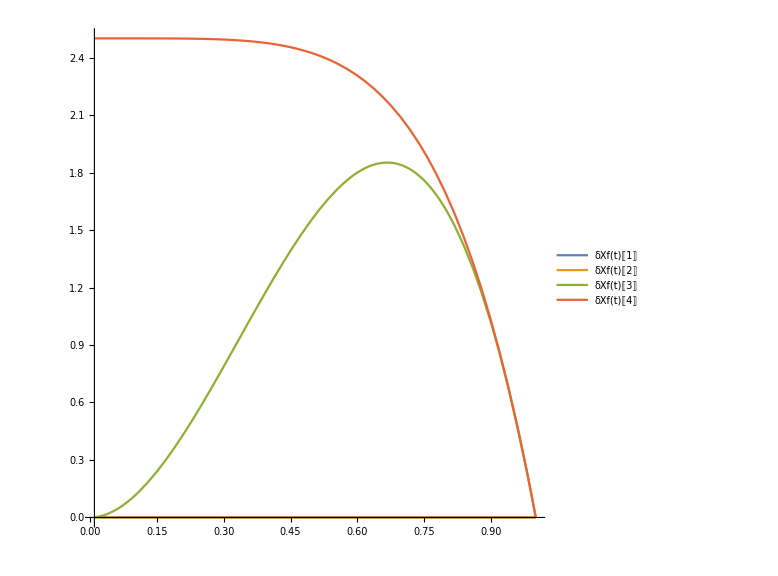

```mathematica
Plot[{δXf[t][[1]],δXf[t][[2]],δXf[t][[3]],δXf[t][[4]]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
δX0[t_]=(F0[t]/αα[t]).δXf[t]/.Join[param,totBG];
δX1[t_]=(F[t][[1]]-F0[t](ββ[t][[1]])/αα[t]).δXf[t]/.Join[param,totBG];
δX2[t_]=(F[t][[2]]-F0[t](ββ[t][[2]])/αα[t]).δXf[t]/.Join[param,totBG];
δX3[t_]=(F[t][[3]]-F0[t](ββ[t][[3]])/αα[t]).δXf[t]/.Join[param,totBG];
```

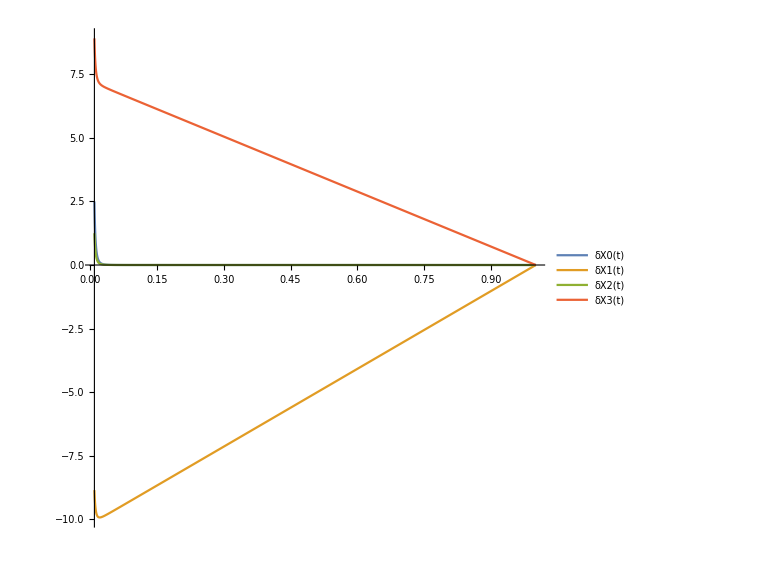

```mathematica
Plot[{δX0[t],δX1[t],δX2[t],δX3[t]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
Δx[t_]=-{δX0[t],δX1[t],δX2[t],δX3[t]}.ndown[t]/.Join[param,totBG];
ξ[t_]=({δX0[t],δX1[t],δX2[t],δX3[t]}-Δx[t]nup[t])/.Join[param,totBG];
```

```mathematica
Δx[ηin]
ξ[ηin]
```

0.000249999999975000122693

{0,-8.854145189105590659552,1.24999999987500061346,8.912476534011198821003}

```mathematica
δXc[t_]={ξ[t][[2]],ξ[t][[3]],ξ[t][[4]]};
trajectory[t_]=Evaluate[{x[t],y[t],z[t]}/.totBG];
Show[ParametricPlot3D[trajectory[η],{η,ηin,ETA0},PlotRange->{{-1,1},{-1,1},{-1,1}}](*/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]]*) ,Table[Graphics3D[{(*{Opacity[η/300+0.28],Black,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(Pu[η]/.totBG))}]},{Opacity[η/300+0.28],Green,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P1[η]/.totBG))}]},{Opacity[η/300+0.28],Blue,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P2[η]/.totBG))}]},{*)(*Opacity[η/300+0.28],*)Red,Arrowheads[0.01],Arrow[{trajectory[η],(trajectory[η]+1/10(δXc[η]/.totBG))}]}],{η,ηin,ETA0,(ETA0-ηin)/30}] , ImageSize->700,AxesLabel->{Style["x/(M̄)",Large],Style["y/(M̄)",Large],Style["z/(M̄)",Large]},AxesStyle->Directive[Black,12],Boxed->False,ViewPoint->{0,100,10}]
```

-Graphics3D-